# CoffeeCode Interface

Set the CoffeeCode release path below (where you execute make), and the file you configured as cc-instance-custom.h during ccmake. You can use the file open dialogue helper to obtain said paths.

Note that depending on whether the build directory is set up with SYMMETRIC_SOLVER or not will NOT determine what variant of CoffeeCode is used to execute the instance; you have to do this manually.

Finally, you’ll have to edit scripts/make-build-dir.sh to activate a valid conda environment for building with a modern gcc. You can remove all the source... blabla lines there if the compilation environment is installed globally anyhow.

```mathematica
SystemDialogInput["Directory"]
SystemDialogInput["FileOpen"]
```

```mathematica
CCRELEASEPATHFULLSOLVER="/home/jkrb2/programming/CoffeeCode/build/release_full/";

RESULTSPATH="/home/jkrb2/Desktop/GraphStateResults/";

PARALLELBUILDPATH="/home/jkrb2/programming/CoffeeCode/build/";
PARALLELBUILDSETUPSCRIPT="/home/jkrb2/programming/CoffeeCode/scripts/make-build-dir.sh";
CCCUSTOMINSTANCEFILE="cc-instance-custom.h";
```

```mathematica
Assert[On];(* enable sanity checks instead of failing silently *)
```

```mathematica
(* avoid race conditions when building in parallel *)
Clear[ParallelBuildDirectory]
ParallelBuildDirectory[]:=Module[{
targetFolder=PARALLELBUILDPATH<>"release-"<>ToString@$SessionID<>"."<>ToString@$KernelID<>"/"
},
If[!DirectoryQ[targetFolder],
Echo["setting up parallel build directory: "<>targetFolder];
RunProcess[{PARALLELBUILDSETUPSCRIPT,targetFolder}] (* bug with commands like "source" *)
];
targetFolder
]
```

```mathematica
ParallelBuildDirectory[]
```

## Basic Graph Functionality [install IGraphM once below, then forget]

### IGraphM

Uncomment the last line in the following cell, then execute to install IGraphM. This only has to be done once per machine.

```mathematica
updateIGraphM[]:=Module[{json,download,target,msg},Check[json=Import["https://api.github.com/repos/szhorvat/IGraphM/releases","JSON"];
download=Lookup[First@Lookup[First[json],"assets"],"browser_download_url"];
msg="Downloading IGraph/M "<>Lookup[First[json],"tag_name"]<>" ...";
target=FileNameJoin[{CreateDirectory[],"IGraphM.paclet"}];
If[$Notebooks,PrintTemporary@Labeled[ProgressIndicator[Appearance->"Necklace"],msg,Right],Print[msg]];
URLSave[download,target],Return[$Failed]];
If[FileExistsQ[target],PacletManager`PacletInstall[target],$Failed]]
(*updateIGraphM[]*) (* uncomment this once and run to install IGraphM locally, then comment again *)
```

```mathematica
<<IGraphM`
ParallelEvaluate[<<IGraphM`;];
```

IGraph/M 0.3.103 (November 13, 2018)

Evaluate IGDocumentation[] to get started.

IGraph/M 0.3.103 (November 13, 2018)

Evaluate IGDocumentation[] to get started.

IGraph/M 0.3.103 (November 13, 2018)

IGraph/M 0.3.103 (November 13, 2018)

IGraph/M 0.3.103 (November 13, 2018)

Evaluate IGDocumentation[] to get started.

Evaluate IGDocumentation[] to get started.

Evaluate IGDocumentation[] to get started.

### Group for Graph State

GroupForGraph gives the full automorphism group of the underlying graph; we color the environment vertices in a different color to make sure the permutation group will be a product across this partitioning.

```mathematica
Clear[GroupForGraph]
GroupForGraph[graph_Graph,kSys_Integer]:=GroupForGraph[graph,kSys]=With[{
kEnv=VertexCount@graph-kSys
},
PermutationGroup[
PermutationCycles/@IGBlissAutomorphismGroup[{graph,"VertexColors"->ConstantArray[0,kSys]~Join~ConstantArray[1,kEnv]}]
]
]
```

```mathematica
(* for iterating over tuples, we'll only need the system vertices subgroup, not the full group *)
```

```mathematica
Clear[Subgroup]
Subgroup[group_PermutationGroup,kSys_Integer]:=Subgroup[group,kSys]=group/.{p_Integer/;p>kSys->Nothing}/.Cycles[{}]->Nothing
```

### Plot Graph

```mathematica
Clear[EnvironmentPlot]
EnvironmentPlot[g_Graph,systemSize_]:=Graph[g,VertexStyle->(
Thread[(Range[VertexCount@g-systemSize]+systemSize)->Red]
),VertexSize->.2,VertexLabels->None]
```

### Create all Possible Choices of Hairs to the Environment

```mathematica
Clear[IsomorphicHairChoiceQ,HairColoring]
HairColoring[hairs_]:=HairColoring[Sort@hairs]=Length/@GroupBy[hairs,Identity]
IsomorphicHairChoiceQ[g_Graph,hairs1_,hairs2_]:=IsomorphicHairChoiceQ[g,hairs1,hairs2]=IsomorphicHairChoiceQ[g,hairs2,hairs1]=IGVF2IsomorphicQ[
{g,"VertexColors"->HairColoring@hairs1},
{g,"VertexColors"->HairColoring@hairs2}
]
IsomorphicHairChoiceQ[g_Graph]:=IsomorphicHairChoiceQ[g,#1,#2]&
```

```mathematica
Clear[HairGraph,AllHairGraphs]
HairGraph[g_,hairs_]:=HairGraph[g,hairs]=With[{
new=VertexCount@g+Range@Length@hairs
},
EdgeList[g]~Join~Thread[hairs<->new]//Graph
]
AllHairGraphs[g_,generator_:Hold[Subsets[#]⟦2;;⟧&]]:=AllHairGraphs[g,generator]=With[{
(* first check for graph isomorphism using a vertex coloring *)
uniqueHairEndpoints=DeleteDuplicates[
ReleaseHold[generator][VertexList@g],
IsomorphicHairChoiceQ[g]
]
},
HairGraph[g,#]&/@uniqueHairEndpoints
]
```

### Strong Generating Set Transversal

```mathematica
Clear[SGSTransversal]
(* the head element of the group stabilizer chain already delivers a transversal of a strong generating set *)
SGSTransversal[group_PermutationGroup]:=With[{
chain=GroupStabilizerChain[group]
},
Partition[chain,2,1]/.{Rule[sA_,gA_],Rule[sB_,gB_]}:>(
Complement[sB,sA]->PermutationGroup@Complement[GroupGenerators@gA,GroupGenerators@gB]
)/.{Rule[s_,PermutationGroup[{}]]:>Nothing}
]
```

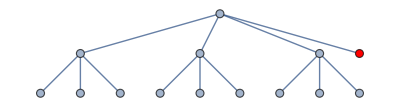
```mathematica
SGSTransversal[GroupForGraph[-Graphics-,13]]
```

### Detecting Products of Symmetric Groups

```mathematica
Clear[ProductOfSymmetricGroupsQ]
ProductOfSymmetricGroupsQ[group_PermutationGroup]:=With[{
orbits=GroupOrbits@group
},
(GroupOrder/@(
GroupStabilizer[group,Complement[Flatten@orbits,#]]&/@orbits
)
)==(Factorial/@Length/@orbits)
]
```

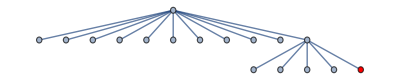
```mathematica
GroupForGraph[-Graphics-,16]
ProductOfSymmetricGroupsQ@%
GroupOrbits@%%
```

```mathematica
GroupForGraph[-Graphics-,13]
ProductOfSymmetricGroupsQ@%
```

```mathematica
Clear[CanonicalizeByOrbits]
(* sort graph vertices such that environment all the way to the right, and orbits of size > 1 come up first *)
CanonicalizeByOrbits[graph_Graph,kSys_Integer]:=With[{
orbits=GroupOrbits[GroupForGraph[graph,kSys],Range@VertexCount@graph],
kTot=VertexCount@graph
},

With[{
coloring=Thread/@MapIndexed[Function[{orbit,i},
(* environment last, length 1 next, nontrivial orbits first; stable sort so add i *)
If[Min@orbit>kSys,
orbit->10kTot+First@i,
If[Length@orbit==1,
orbit->5kTot+First@i,
orbit->First@i
]]
],orbits]//Flatten//SortBy[First]
},
Graph[
IGBlissCanonicalGraph[{graph,"VertexColors"->Last/@coloring}],
VertexLabels->"Index"
]
]
]
```

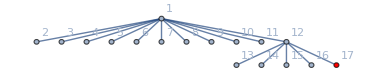
```mathematica
CanonicalizeByOrbits[-Graphics-,16]
```

### Detecting whether one orbit has multiple hairs

```mathematica
Clear[OrbitsHaveMultipleHairsQ]
OrbitsHaveMultipleHairsQ[group_PermutationGroup,g_Graph,kSys_Integer]:=Module[{
environmentVertices=VertexList[g]⟦kSys+1;;⟧,
hairNeighbourIndices
},
hairNeighbourIndices=VertexIndex[g,#]&/@VertexList@Subgraph[NeighborhoodGraph[g,environmentVertices],Complement[VertexList@g,environmentVertices]];

Intersection[#,hairNeighbourIndices]&/@GroupOrbits[group]//AnyTrue[#,Length@##>1&]&
]
```

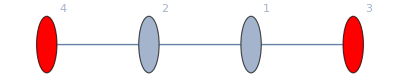
```mathematica
-Graphics-
Subgroup[GroupForGraph[%,2],2]
OrbitsHaveMultipleHairsQ[%,%%,2]
```

## CoffeeCode Link

### Exporting MM symbols

```mathematica
Clear[ExportAdjacencyMatrix]
ExportAdjacencyMatrix[g_Graph]:=With[{
Avec=g//AdjacencyMatrix//Normal//Flatten
},
StringJoin[ToString/@Avec]
]
```

```mathematica
Clear[SGSTransversalMMForm]
SGSTransversalMMForm[list_List,kSys_Integer]:=list/.{
Rule[{idx_Integer},PermutationGroup[cycles_List]]:>Module[{
permutationIndices=PermutationList[#,kSys]&/@cycles
},

(* the pivot point is the first index for which the SGSGenerator acts nontrivially on (so one point past the points that are stabilized).
If the pivot point for the SGSGenerator is 2, that means we want to check indices 0 and 1 in C++; in MM this would correspond to indices {1, 2}, which is what ⟦;;2⟧ truncates to.
Therefore we validly don't subtract 1 from the pivot point, but do subtract 1 from all other indices *)
StringRiffle[Flatten@{
"\tSGSGenerator<"<>ToString@(#1)<>", Group<",
("\t\tPermutation<"<>StringRiffle[ToString/@(##-1),","]<>">")&/@#2,
"\t>>"
},"\n"]&@@{idx,permutationIndices}

]
}//Flatten//("using sgs = SGSTransversal<\n"<>StringRiffle[#,",\n"]<>"\n>;")&

(* for the trivial transversal we simply pass an orbit, sort the graph canonically etc *)
Clear[TrivialSGSTransversalMMForm]
TrivialSGSTransversalMMForm[list_List,kSys_Integer]:=With[{
orbits=list/.{n_Integer}:>Nothing//SortBy[First]
},
With[{
lengths=Accumulate[Length/@orbits]
},
With[{
orbitBounds={0}~Join~lengths//Partition[#,2,1]&
},

StringRiffle[(
"\tTrivialSGSOrbit<"<>ToString[#1]<>", "<>ToString[#2]<>">"
)&@@@orbitBounds,
",\n"]
]//("using sgs = TrivialSGSTransversal<"<>ToString[kSys]<>",\n"<>#<>"\n>;")&
]
]
```

```mathematica
Subgroup[GroupForGraph[-Graphics-,2],2]
TrivialSGSTransversalMMForm[GroupOrbits@%,2]
```

```mathematica
Clear[ExportSymmetricCCInstance]
ExportSymmetricCCInstance[graph_Graph,kSys_Integer,name_:"graphstate_instance"]:=With[{
group=Subgroup[GroupForGraph[graph,kSys],kSys],
kTot=VertexCount@graph
},

If[!OrbitsHaveMultipleHairsQ[group,graph,kSys]∧ProductOfSymmetricGroupsQ@group,
(* write Orbits as expected for TrivialSGS Solver *)
With[{
orbits=GroupOrbits@group,
graphCanonicalized=CanonicalizeByOrbits[graph,kSys]
},

If[Length@orbits==0∨Max[Length/@orbits]==1,Echo["WARN: symmetry group is 0. Not a valid symmetric problem instance."];Throw["invalid instance"]
];
Echo["Product symmetry group with single hairs detected. Compiling for trivial canonical image provider."];

"struct "<>name<>" {\n"<>
TrivialSGSTransversalMMForm[orbits,kSys]<>"\n"<>
"constexpr static size_t k_sys = "<>ToString[kSys]<>", k_env = "<>ToString[kTot-kSys]<>";\n"<>
"constexpr static AdjacencyMatrixT<"<>ToString[kTot]<>"> adjacency_matrix{"<>ToString[Normal@AdjacencyMatrix@graphCanonicalized]<>"};\n"<>
"};"
]
,
(* write SGSGenerators as expected for Nauty *)
With[{
sgs=SGSTransversal@group
},

If[Length@sgs==0,Echo["WARN: symmetry group is 0. Not a valid symmetric problem instance."];
Throw["invalid instance"]
];
Echo["Nested symmetry group or multiple hairs per orbit detected. Compiling for nauty's canonical image provider."];

"struct "<>name<>" {\n"<>
SGSTransversalMMForm[sgs,kSys]<>"\n"<>
"constexpr static size_t k_sys = "<>ToString[kSys]<>", k_env = "<>ToString[kTot-kSys]<>";\n"<>
"constexpr static AdjacencyMatrixT<"<>ToString[kTot]<>"> adjacency_matrix{"<>ToString[Normal@AdjacencyMatrix@graph]<>"};\n"<>
"};"
]
]
]
```

### Build Interface

```mathematica
Clear[MakeCC]
MakeCC[kSys_Integer,kEnv_Integer]:=With[{
out=RunProcess[
{
"make",
"-B",
"K_SYS="<>ToString@kSys,
"K_ENV="<>ToString@kEnv
},
ProcessDirectory->ParallelBuildDirectory[]
]
},
If[out["ExitCode"]≠0∨out["StandardError"]≠"",Echo[out];Throw["make error"]];
]
MakeCC[graph_Graph,kSys_Integer]:=With[{
instanceFileContent=ExportSymmetricCCInstance[graph,kSys]
},

Export[ParallelBuildDirectory[]<>CCCUSTOMINSTANCEFILE,instanceFileContent,"Text"];
MakeCC[kSys,VertexCount@graph-kSys]
]
```

```mathematica
MakeCC[9,1]
```

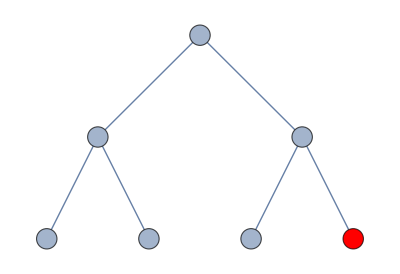
```mathematica
MakeCC[-Graphics-,6]
```

```mathematica
Clear[RunCC]
RunCC[graph_Graph,kSys_Integer]:=With[{},
If[!MakeCC[graph,kSys],Return[False]];

With[{
ccResult=RunProcess["CoffeeCode",All,ProcessDirectory->ParallelBuildDirectory[]]
},
If[ccResult["ExitCode"]≠0∨ccResult["StandardError"]≠"",Echo[ccResult];Throw["run error"]];

ImportString[ccResult["StandardOutput"],"RawJSON"]
]
]
```

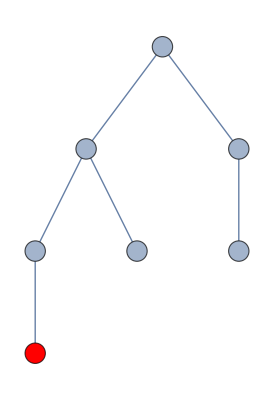
```mathematica
RunCC[-Graphics-,6]
```

### Full Solver Interface

```mathematica
Clear[CCPath]
CCPath[kSys_Integer,kEnv_Integer]:=CCPath[kSys,kEnv]=CCRELEASEPATHFULLSOLVER<>"CoffeeCode."<>ToString[kSys]<>"."<>ToString[kEnv]

(* RunCC overload *)
RunCC[graph_Graph,kSys_Integer,"Full"]:=Module[{
adjacencyMatrix=ExportAdjacencyMatrix@graph,
kEnv=VertexCount@graph-kSys
},
With[{
executable=CCPath[kSys,kEnv]
},

Assert[FileExistsQ[executable]];

With[{
ccResult=RunProcess[executable,All,adjacencyMatrix]
},
If[ccResult["ExitCode"]≠0∨ccResult["StandardError"]≠"",Echo[ccResult];Throw["run error"]];

ImportString[ccResult["StandardOutput"],"RawJSON"]
]
]
]
```

```mathematica
RunCC[-Graphics-,6,"Full"]
```

### Importing JSON format

```mathematica
Clear[MultArrayToPoly]
MultArrayToPoly[{mult_,list_}]:={
mult,
MapIndexed[f,list]/.f[coeff_,{exponent_}]:>coeff q^(exponent-1)//Total
}
```

```mathematica
Clear[PauliActionCC]
PauliActionCC[graph_Graph,kSys_Integer,p_,symmetricSolver_:True]:=Module[{
kTot=VertexCount@graph,
kEnv=VertexCount@graph-kSys,

pp={1-p,p/3,p/3,p/3},
λ,λa,λm,λma
},

If[kEnv>kSys∨kSys<1∨kTot<2,Throw["invalid params"]];

(* get lambda and lambda_a *)
{{λm,λ},{λma,λa}}=With[{
result=If[symmetricSolver,
RunCC[graph,kSys],
RunCC[graph,kSys,"Full"]
]
},

{
MultArrayToPoly/@result["lambda"]//Transpose,
MultArrayToPoly/@result["lambda_a"]//Transpose
}
];

(* final expression in the variables given *)
Thread/@Thread[(
p0^kSys{λ,λa/2^(kTot-kSys)}/.{
p0->pp⟦1⟧,
q->pp⟦2⟧/pp⟦1⟧
}//Simplify
)->{λm,λma}
]
]
```

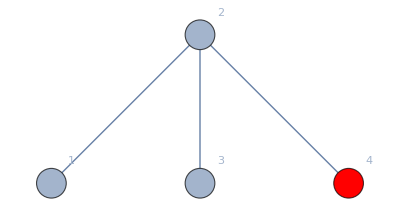
```mathematica
PauliActionCC[-Graphics-,3,p]
```

## Entropy and CI

```mathematica
Clear[ShannonEntropyMult,CIMult]
ShannonEntropyMult[l_List]:=l/.Rule[0,_]:>0/.Rule[term_,mult_]:>-mult*term Log2[term]//Total
CIMult[λ_,λa_]:=(ShannonEntropyMult[λa]-ShannonEntropyMult[λ])/Log2@Total@(Last/@List@@λa)
```

```mathematica
Clear[CIThreshold]
CIThreshold[g_Graph,kSys_Integer,symmetricSolver_:True]:=With[{
pa=PauliActionCC[g,kSys,p,symmetricSolver]
},
FindRoot[CIMult@@pa,{p,.2}]
]
```

## Interface

### Manual Export

#### Create graphs by hand

To create graphs by hand, look up the following functions:

```mathematica
AdjacencyGraph
SparseArray
PathGraph
```

Or directly use MM’s Graph object, where edges are entered with ESC ue ESC

```mathematica
Graph[{1<->2,3<->4,3<->5,1<->3}]
```

#### Create a random graph, add a hair, and plot.

```mathematica
CompleteGraph[10];
HairGraph[%,{10,9}];
graph=EnvironmentPlot[%,10]
```

#### Export instance

Just adjacency matrix for Full Solver

```mathematica
ExportAdjacencyMatrix[-Graphics-]
```

SGS for Symmetric Solver

```mathematica
ExportSymmetricCCInstance[-Graphics-,16]
```

### Automatic Export, Build and Import

#### Get CI for a Graph

This is now a single line. Remove the semicolon to see full analytic expression.

```mathematica
CIMult@@PauliActionCC[-Graphics-,3,p];
```

For plotting, use e.g.

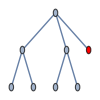
```mathematica
CIMult@@PauliActionCC[-Graphics-,7,p];
Plot[%,{p,0,1}]
```

The same graph is small enough to be faster with the full solver:

```mathematica
CIMult@@PauliActionCC[-Graphics-,7,p,False];
Plot[%,{p,0,1}]
```

If the symmetry group is 0, we cannot solve with the symmetric solvers; an error is thrown that you can catch.

```mathematica
Catch@CIThreshold[-Graphics-,6]
```

Solving fully still works.

```mathematica
Catch@CIThreshold[-Graphics-,6,False]
```

## Some Graph Classes

### Rooted Graph Product/Concatenated Codes

```mathematica
Clear[ConcatGraph]
ConcatGraph[g1_Graph,g2_Graph,v1_Integer,v2_Integer]:=With[{
vcount1=VertexCount@g1,
vertices2=VertexList@g2,
edges2=EdgeList@g2
},
With[{
vmap=If[#==v2,v1,If[#<v2,#+vcount1,#+vcount1-1]]&
},
GraphUnion[g1,Graph[vmap/@vertices2,Map[vmap,edges2,{2}]]]
]
]

ConcatGraph[g1_Graph,g2_Graph,v1_List,v2_Integer]:=
Fold[f,{g1,g2,v2},v1]//.f[{gg1_,gg2_,vv2_},vv1_]:>{ConcatGraph[gg1,gg2,vv1,vv2],gg2,vv2}//First
```

### Tristar Graphs

#### Graph Generation

A tristar graph is like a bistar graph but with two leg bushles; there is six distinct choices of fitting a single hair onto it

```mathematica
Clear[TristarGraph]
TristarGraph[n_,na_,nb_]:=With[{
nna=Max[na,nb],
nnb=Min[na,nb]
},

With[{
g=StarGraph[n],
ga=StarGraph[nna],
gb=StarGraph[nnb]
},
ConcatGraph[
ConcatGraph[g,ga,{2},1],
gb,{3},1
]
]]
```

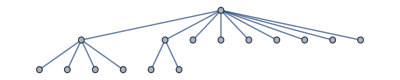

16

```mathematica
TristarGraph[10,5,3]
VertexCount@%
```

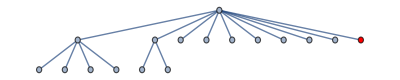
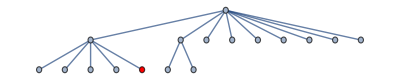
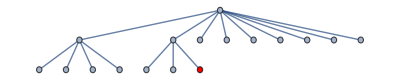
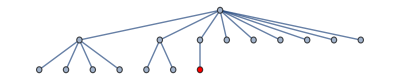
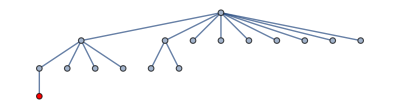
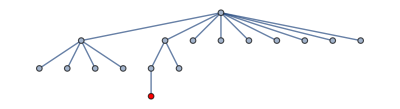

```mathematica
EnvironmentPlot[#,VertexCount@#-1]&/@AllHairGraphs[TristarGraph[10,5,3],Subsets[#,{1}]&]
```

Because this is generally slow, we produce all hair codes separately as per below.

```mathematica
Clear[AllHairGraphsTristarGraph]
AllHairGraphsTristarGraph[g_Graph,{n_Integer,na_Integer,nb_Integer}]:=HairGraph[g,{#}]&/@{1,2,3,4,n+1,n+Max[na,nb]}
```

```mathematica
Clear[AllTristarGraphs]
AllTristarGraphs[n_]:=With[{
args=DeleteCases[
IntegerPartitions[n,{3},Range[2,n]],
{_,a_,a_}(* delete cases where two bushles are the same size *)
]
},
Map[Function[arg,
arg->(
EnvironmentPlot[#,Total@arg-2]&/@(
AllHairGraphsTristarGraph[TristarGraph@@arg,#]&@arg
)
)
],args]//Association
]

AllTristarGraphs[10]
```

#### Exhaustive Search

```mathematica
searchResults=Table[{i,AllTristarGraphs[i]},{i,8,63}]/.{i_Integer,a_Association}:>With[{
results=KeyValueMap[Function[{sizes,graphs},
<|"sizes"->sizes,"graph"->#,"p"->(p/.CIThreshold[#,VertexCount@#-1,False])|>&/@graphs
],a]//Flatten,
exportFilename=RESULTSPATH<>"tristar."<>ToString@i<>".thresholds"
},
Put[results,exportFilename];
Echo[MaximalBy[results,#⟦"p"⟧&],"best for "<>ToString[i]]
];
```

Parallelize::nopar1: … cannot be parallelized; proceeding with sequential evaluation.

best for 8 {<|sizes→{3,3,2},graph→-Graphics-,p→0.18941,error→False|>}

Parallelize::nopar1: … cannot be parallelized; proceeding with sequential evaluation.

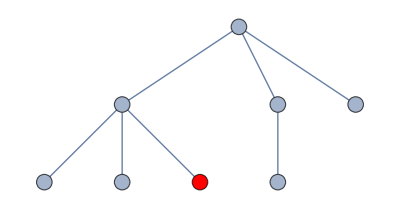
best for 9 {<|sizes→{4,3,2},graph→-Graphics-,p→0.189548,error→False|>}

Parallelize::nopar1: … cannot be parallelized; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::nopar1 will be suppressed during this calculation.

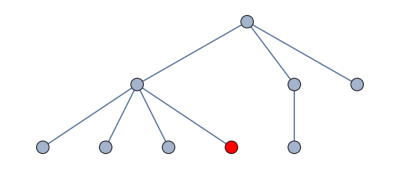
best for 10 {<|sizes→{4,4,2},graph→-Graphics-,p→0.189743,error→False|>}

$Aborted

```mathematica
searchResults=ParallelTable[{i,AllTristarGraphs[i]},{i,8,63}]/.{i_Integer,a_Association}:>With[{
results=KeyValueMap[Function[{sizes,graphs},
ParallelMap[With[{
ci=Catch[
p/.CIThreshold[#,VertexCount@#-1,i>15]
]
},
<|
"sizes"->sizes,
"graph"->#,
"p"->If[NumericQ[ci],ci,-1],
"error"->If[NumericQ[ci],False,ci]
|>
]&,graphs]
],a]//Flatten,
exportFilename=RESULTSPATH<>"tristar."<>ToString@i<>".thresholds"
},
Put[results,exportFilename];
Echo[MaximalBy[results,#⟦"p"⟧&],"best for "<>ToString[i]]
];
```